```mathematica
NewtonsMethod[f_,ϵ_,x0_]:=Block[{xk=x0,newXk,coef,iterCount=0},
While[True,
(*В некоторых случаях мы не можем обратить якобиан*)
newXk=xk-(f/.x->xk)/(D[f,x]/.x->xk);
coef=Norm[newXk-xk];
xk=newXk;
iterCount++;
If[coef<ϵ,Break[]]];Return[newXk];]
```

```mathematica
progonka[H_,values_]:=Module[{n=Length[H],v =Table[0,{k,1,n}],u = Table[0,{k,1,n}],x },
v[[1]]=H[[1]][[2]]/(-H[[1]][[1]]);
u[[1]]=(-values[[1]])/(-H[[1]][[1]]);
For[k=2,k<=n-1,++k,
v[[k]]=H[[k]][[k+1]]/(-H[[k]][[k]]-H[[k]][[k-1]]*v[[k-1]]);
u[[k]]=(H[[k]][[k-1]]*u[[k-1]]-values[[k]])/(-H[[k]][[k]]-H[[k]][[k-1]]*v[[k-1]]);];
v[[n]]=0;
u[[n]]= (H[[n]][[n-1]]*u[[n-1]]-values[[n]])/(-H[[n]][[n]]-H[[n]][[n-1]]*v[[n-1]]);
x[[n]]=u[[n]];
For[k = n, k>1,--i,
x[[k-1]]=v[[k-1]]*x[[k]]+u[[k-1]]];
Return[x];]
```

### Константы

```mathematica
A=-0.024 (**);
B=1.69 (**);
CC=0.5 (**);
α=10^-5 (*K-1*);
T0=300 (*K*);
(*Subscript[T, avg]=300 (*K*);*)
Young=1.75*10^11 (*Па*);
σf=1.1*10^8 (*Па*);
ϵf=0.000628571;
l=10(*Длина стержня*);
Tf=20(*Конечный момент времени*);
τ=0.005 (*Шаг времени*);
a=50 (*Просто константа*);
n=11 (*Число узлов сетки*);
```

### Необходимые функции

```mathematica
F[x_] := a Sin[(π x)/l];
T1 [x_,t_]:=T0+F[x]t Sin[t];
T2[x_,t_]:=T0+F[x]Cos[π t^2](t+1);
TT=T1;
ϵT[T_]:=α (T-T0);
ϵ[u_]:=D[u,x];
```

### Аналитическое решение

```mathematica
uAnalytical = 
	First[Flatten[
DSolve[{
D[D[u[x,t], x]-ϵT[TT[x,t]], x]== 0,
u[0, t] == 0, 
u[l, t] == 0},
u[x,t],{x, t}]]
]⟦2⟧  // FullSimplify
```

-(t (-5+x+5 Cos[(π x)/10]) Sin[t])/(1000 π)

```mathematica
εAnalytical = D[uAnalytical,x]/.x->2;
```

```mathematica
εeAnalytical = εAnalytical-ϵT[TT[2,t]];
```

```mathematica
sigmaAnalytical = Young*εeAnalytical;
```

(u_(i+1)-2 u_i+u_(i-1))/h^2=α ∂/(∂x)(F[x]*Tau[t]) = f

```mathematica
f = D[ϵT[TT[x,t]],x];
```

```mathematica
If[NumberQ[n],
h=l/(n-1),
If[NumberQ[h],n=IntegerPart[l/h];h=l/n]
];
```

#### Создаем узлы (точки)

```mathematica
points = Table[i*h,{i,0,n-1}];
```

#### Значения правой части

```mathematica
values={0}~Join~Table[f/.{x->points[[i]]},{i,2,n-1}]~Join~{0};
```

```mathematica
(*H = Table[Table[
If [i ==j,-2/h^2,If[i==j+1 || j==i+1,1/h^2,0]],
{i,0,n-1}],
{j,0,n-1}];*)
```

```mathematica
H=Table[Table[
If [i ==j,
If[i == 0||i == n-1,1,-2/h^2],
If[(i == j-1||i == j+1)&&j≠0&&j≠n-1,1/h^2,0 ]],
{i,0,n-1}],
{j,0,n-1}];
H//MatrixForm;
```

```mathematica
(*progonka[H,values]*)
```

```mathematica
uNumerical =LinearSolve[H,values];
```

### Полные деформации (∂u)/(∂x) ≈ (u_numerical[[i+1]]-u_numerical[[i-1]])/(2h)

```mathematica
duNumerical = {0}~Join~Table[(uNumerical[[i+1]]-uNumerical[[i-1]])/(2h),{i,2,n-1}]~Join~{0}//N;
```

```mathematica
Length[duNumerical];
```

### Решение на каждом временном слое

```mathematica
σ=Table[0,{i,1,n}];
σfv=Table[σf,{i,1,n}];
ϵ=Table[0,{i,1,n}];
ϵe=Table[0,{i,1,n}];
ϵcrk=Table[0,{i,1,n}];
T=Table[0,{i,1,n}];
```

```mathematica
data={};
For[tt=0,tt<=Tf,tt=tt+τ,
temp={};
For [i=1,i<=n,++i,
T⟦i⟧=TT[points⟦i⟧,tt];
ϵ⟦i⟧=duNumerical⟦i⟧/.t->tt;
ϵe⟦i⟧=ϵ⟦i⟧ -ϵT[T[[i]]]-ϵcrk⟦i⟧/.t->tt;
If[Young*ϵe⟦i⟧ <σfv⟦i⟧,
σ⟦i⟧ =  Young*ϵe⟦i⟧,
σfv[[i]] =  σf*( A+B*Exp[-CC*(ϵ[[i]]-ϵT[T[[i]]])/ϵf]);
σ[[i]]=σfv[[i]];
ϵcrk[[i]]=ϵ⟦i⟧-ϵT[T[[i]]]-σ⟦i⟧/Young;
(*σfv[[i]] =  σf*( A+B*Exp[-CC*(ϵ[[i]]-ϵT[T[[i]]])/ϵf]);
σ[[i]]=σfv[[i]];
ϵcrk⟦i⟧=ϵ⟦i⟧-ϵT[T[[i]]]-σ⟦i⟧/Young;
(*ϵe[[i]]=(First@Flatten@Solve[σf(A+B*Exp[-CC*(x+ϵcrk[[i]])/ϵf])==σfv[[i]],x])[[2]];*);
g[x_]:=σf(A+B*Exp[-CC*(x+ϵcrk[[i]])/ϵf])-σfv[[i]];
ϵe[[i]] = NewtonsMethod[g[x],10^-7,-0.0015869299334807826];*)
];
(*Print[ϵe[[i]]];*)
AppendTo[temp,{tt,T⟦i⟧,σ⟦i⟧,ϵ⟦i⟧,ϵ⟦i⟧- ϵT[T[[i]]],ϵcrk⟦i⟧,ϵe[[i]],i}]
];
 AppendTo[data,temp]
 ];
```

```mathematica
data;
```

## Графики

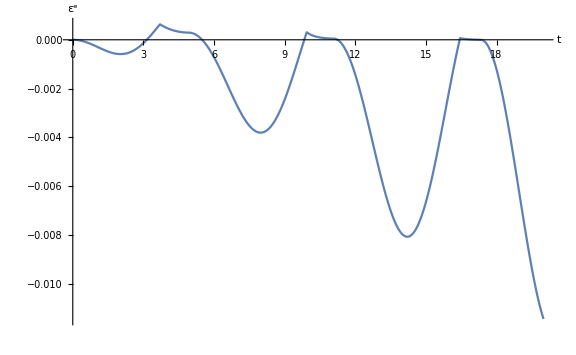

```mathematica
times = IntegerPart[Tf/τ];
tϵe=ListPlot[Table[{data⟦i,2,1⟧,data⟦i,2,7⟧},{i,1,times }],Joined->True,ImageSize->Large,AxesLabel->{Style["t",Large],Style["ε^e",Large]},AxesStyle->Directive[Black, 14]]
```

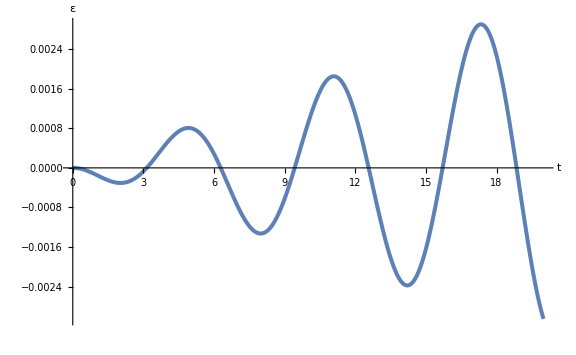

```mathematica
tϵ=ListPlot[Table[{data⟦i,2,1⟧,data⟦i,2,4⟧},{i,1,times }],Joined->True,ImageSize->Large,AxesLabel->{Style["t",Large],Style["ε",Large]},AxesStyle->Directive[Black, 14],PlotStyle->Thickness[0.005]]
```

```mathematica
ListPlot[Table[{data⟦i,2,1⟧,(A+B Exp[-CC data⟦i,2,4⟧/ϵf])*σf},{i,1,times }],Joined->True,ImageSize->Large,AxesLabel->{Style["t",Large],Style["σ",Large]},AxesStyle->Directive[Black, 14]];
```

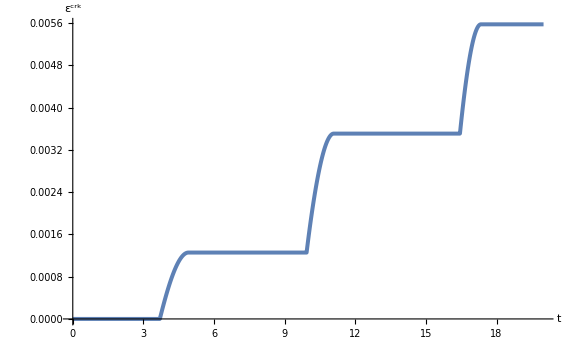

```mathematica
tϵcrk=ListPlot[Table[{data⟦i,2,1⟧,data⟦i,2,6⟧},{i,1,times }],Joined->True,ImageSize->Large,AxesLabel->{Style["t",Large],Style["ε^crk",Large]},AxesStyle->Directive[Black, 14],PlotRange->All,PlotStyle->Thickness[0.005]]
```

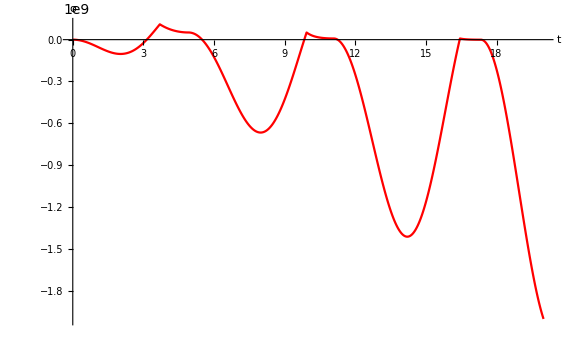

```mathematica
tσ=ListPlot[Table[{data⟦i,2,1⟧,data⟦i,2,3⟧},{i,1,times }],Joined->True,ImageSize->Large,AxesLabel->{Style["t",Large],Style["σ",Large]},AxesStyle->Directive[Black, 14],PlotRange->All,PlotStyle->Red]
```

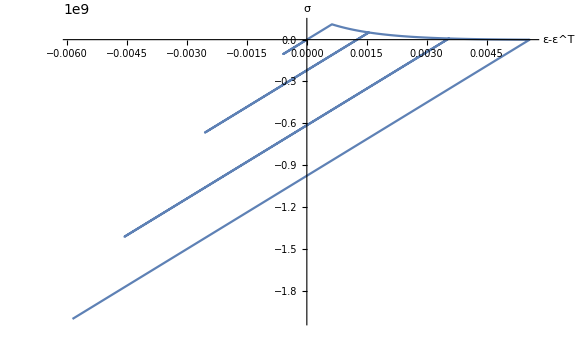

```mathematica
dϵσ=ListPlot[Table[{data⟦i,2,5⟧,data⟦i,2,3⟧},{i,1,times }],Joined->True,ImageSize->Large,AxesLabel->{Style["ε-ε^T",Large],Style["σ",Large]},AxesStyle->Directive[Black, 11]]
```

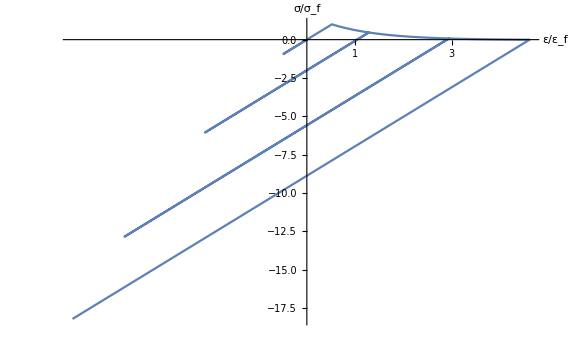

```mathematica
normϵσ=ListPlot[Table[{data⟦i,2,4⟧/ϵf,data⟦i,2,3⟧/σf},{i,1,times }],Joined->True,ImageSize->Large,AxesLabel->{Style["ε/ε_f",Large],Style["σ/σ_f",Large]},AxesStyle->Directive[Black, 14],Ticks->{Table[i,{i,1,10}],Automatic},PlotRange->Full]
```

```mathematica
Plot[A+B Exp[-C*εAnalytical/ϵf],{t,1,20},PlotRange->Full];
```

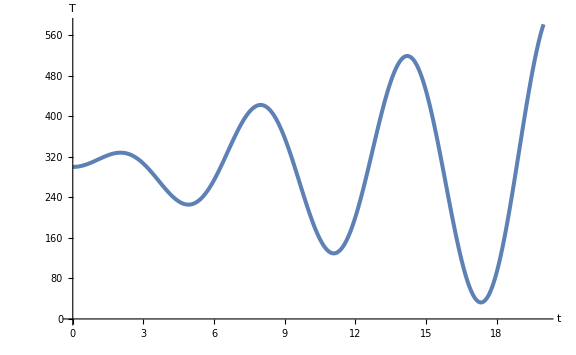

```mathematica
tT=ListPlot[Table[{data⟦i,2,1⟧,data⟦i,2,2⟧},{i,1,times }],Joined->True,ImageSize->Large,AxesLabel->{Style["t",Large],Style["T",Large]},AxesStyle->Directive[Black, 14],PlotStyle->Thickness[0.005]]
```

### Переход от линейности к излому

```mathematica
Manipulate[ListPlot[Table[{data⟦i,2,1⟧,data⟦i,2,4⟧},{i,1,j}],Joined->True,ImageSize->Large,AxesLabel->{"t","ε"},AxesStyle->Directive[Black, 14]],{j,1,times}];
```

```mathematica
Manipulate[ListPlot[Table[{data⟦i,2,1⟧,data⟦i,2,6⟧},{i,1,j}],Joined->True,ImageSize->Large,AxesLabel->{"t","ε^crk"},AxesStyle->Directive[Black, 14]],{j,1,times}];
```

```mathematica
Manipulate[ListPlot[Table[{data⟦i,2,1⟧,data⟦i,2,3⟧},{i,1,j}],Joined->True,ImageSize->Large,AxesLabel->{"t","σ"},AxesStyle->Directive[Black, 14]],{j,1,times}];
```

```mathematica
Manipulate[ListPlot[Table[{data⟦i,2,5⟧,data⟦i,2,3⟧},{i,1,j}],Joined->True,ImageSize->Large,AxesLabel->{"ε-ε^T","σ"},AxesStyle->Directive[Black, 14]],{j,1,times}];
```

```mathematica
Manipulate[ListPlot[Table[{data⟦i,2,4⟧/ϵf,data⟦i,2,3⟧/σf},{i,1,j }],Joined->True,ImageSize->Large,AxesLabel->{"ε/ε_f","σ/σ_f"},AxesStyle->Directive[Black, 14],Ticks->{Table[i,{i,1,10}],Automatic},PlotRange->Full],{j,1,times}];
```

```mathematica
Manipulate[ListPlot[Table[{data⟦i,2,1⟧,data⟦i,2,2⟧},{i,1,j}],Joined->True,ImageSize->Large,AxesLabel->{"t","T"},AxesStyle->Directive[Black, 14]],{j,1,times}];
```

### Проверка порядка точности

```mathematica
uAnalytical
```

-(t (-5+x+5 Cos[(π x)/10]) Sin[t])/(1000 π)

```mathematica
uNumerical
```

{0,(-π t Sin[t]-2 √5 π t Sin[t]-√(2 (5-√5)) π t Sin[t]-2 √(2 (5+√5)) π t Sin[t])/200000,(-4 π t Sin[t]-8 √5 π t Sin[t]-4 √(2 (5-√5)) π t Sin[t]-3 √(2 (5+√5)) π t Sin[t])/400000,(-π t Sin[t]-7 √5 π t Sin[t]-6 √(2 (5-√5)) π t Sin[t]-2 √(2 (5+√5)) π t Sin[t])/400000,(2 π t Sin[t]-6 √5 π t Sin[t]-3 √(2 (5-√5)) π t Sin[t]-√(2 (5+√5)) π t Sin[t])/400000,0,(-2 π t Sin[t]+6 √5 π t Sin[t]+3 √(2 (5-√5)) π t Sin[t]+√(2 (5+√5)) π t Sin[t])/400000,(π t Sin[t]+7 √5 π t Sin[t]+6 √(2 (5-√5)) π t Sin[t]+2 √(2 (5+√5)) π t Sin[t])/400000,(4 π t Sin[t]+8 √5 π t Sin[t]+4 √(2 (5-√5)) π t Sin[t]+3 √(2 (5+√5)) π t Sin[t])/400000,(π t Sin[t]+2 √5 π t Sin[t]+√(2 (5-√5)) π t Sin[t]+2 √(2 (5+√5)) π t Sin[t])/200000,0}

```mathematica
points;
```

```mathematica
pN2 = uNumerical[[2]];
```

```mathematica
pA2 = uAnalytical/.x->1h;
```

```mathematica
Manipulate[Plot[{uNumerical[[i+1]],uAnalytical/.x->i*h},{t,0,Tf}],{i,0,n-1,1}]
```

```mathematica
Manipulate[Max[Abs[(uNumerical[[i+1]]-(uAnalytical/.x->i*h))/.t->1]],{i,0,n-1,1}]//N
```

```mathematica
Max[Table[Abs[(uNumerical[[i+1]]-(uAnalytical/.x->i*h))/.t->1],{i,0,n-1,1}]//N]
```

2.31369×10^-6

```mathematica
(1.4489379997781413*^-7)/(3.6215070848037104*^-8)
```

4.00093

```mathematica
(9.276900963075315*^-8)/(2.31888189376815*^-8)
```

4.00059